```mathematica
repNullAtLeast= Table[allGraphs5[k,"colofourrealnull"]->allGraphs5[k,"atleast"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5→34,n12x3x4x5→13,n123x4x5→5,n1234x5→2,n12345→1,n1235x4→2,n123x45→2,n124x3x5→4,n1245x3→2,n124x35→1,n125x3x4→5,n125x34→2,n12x34x5→5,n12x345→2,n12x35x4→4,n12x3x45→5,n13x2x4x5→10,n134x2x5→4,n1345x2→2,n134x25→1,n135x2x4→4,n135x24→1,n13x24x5→2,n13x245→1,n13x25x4→2,n13x2x45→4,n14x2x3x5→10,n145x2x3→5,n145x23→2,n14x23x5→4,n14x235→1,n14x25x3→2,n14x2x35→2,n15x2x3x4→13,n15x23x4→5,n15x234→2,n15x24x3→4,n15x2x34→5,n1x23x4x5→13,n1x234x5→5,n1x2345→2,n1x235x4→4,n1x23x45→5,n1x24x3x5→10,n1x245x3→4,n1x24x35→2,n1x25x3x4→10,n1x25x34→4,n1x2x34x5→13,n1x2x345→5,n1x2x35x4→10,n1x2x3x45→13}

```mathematica
tooLow=Select[Keys[allGraphs5],((allGraphs5[#,"colofourrealnull"]/.repNullAtLeast)-allGraphs5[#,"atleast"])<0&]
```

{29511,29520,29523,29524,29521,29514,29515,29512,29496,29497,29487,29488,29442,29443,29433,29434,29268,29277,29280,29281,29278,29271,29272,29269,29253,29254,29244,29245,29199,29200,29190,29191,28782,28791,28794,28795,28792,28785,28786,28783,28767,28768,28758,28759,28713,28714,28704,28705,28539,28548,28551,28552,28549,28542,28543,28540,28524,28525,28515,28516,28470,28471,28461,28462,27336,27337,27327,27328,27093,27094,27084,27085,26607,26608,26598,26599,26364,26365,26355,26356,22962,22963,22953,22954,22719,22720,22710,22711,22233,22234,22224,22225,21990,21991,21981,21982,9828,9837,9840,9841,9838,9831,9832,9829,9813,9814,9804,9805,9759,9760,9750,9751,9585,9594,9597,9598,9595,9588,9589,9586,9570,9571,9561,9562,9516,9517,9507,9508,9099,9108,9111,9112,9109,9102,9103,9100,9084,9085,9075,9076,9030,9031,9021,9022,8856,8865,8868,8869,8866,8859,8860,8857,8841,8842,8832,8833,8787,8788,8778,8779,7653,7654,7644,7645,7410,7411,7401,7402,6924,6925,6915,6916,6681,6682,6672,6673,3279,3280,3270,3271,3036,3037,3027,3028,2550,2551,2541,2542,2307,2308,2298,2299}

```mathematica
tooHigh=Select[Keys[allGraphs5],((allGraphs5[#,"colofourrealnull"]/.repNullAtLeast)-allGraphs5[#,"atleast"])>0&];
```

```mathematica
Length[tooHigh]
```

280

```mathematica
FactorInteger[1729]
```

{{7,1},{13,1},{19,1}}

```mathematica
Table[((allGraphs5[k,"colofourrealnull"]/.repNullAtLeast)-allGraphs5[k,"atleast"]) ->ShowGraph5Least[k],{k,tooLow}]//Sort
```

```mathematica
Table[((allGraphs5[k,"colofourrealnull"]/.repNullAtLeast)-allGraphs5[k,"atleast"]) ->ShowGraph5Least[k],{k,tooHigh}]//Sort
```

```mathematica
nullAtoms=Sort[Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}],CompareSymbols]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3,n12x345,n123x45,n124x35,n125x34,n13x245,n134x25,n135x24,n14x235,n145x23,n15x234,n1x2345,n1234x5,n1235x4,n1245x3,n1345x2,n12345}

```mathematica
fakenullAtoms=Sort[Table[allGraphs5[k,"colofournull"],{k,allGraphs5FakeAtomKeys}],CompareSymbols]
```

{p1x2x3x4x5,p1x2x3x45,p1x2x34x5,p1x2x35x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x45,p1x24x35,p1x25x34,p12x3x45,p12x34x5,p12x35x4,p13x2x45,p13x24x5,p13x25x4,p14x2x35,p14x23x5,p14x25x3,p15x2x34,p15x23x4,p15x24x3,p1x2x345,p1x234x5,p1x235x4,p1x245x3,p123x4x5,p124x3x5,p125x3x4,p134x2x5,p135x2x4,p145x2x3,p12x345,p123x45,p124x35,p125x34,p13x245,p134x25,p135x24,p14x235,p145x23,p15x234,p1x2345,p1234x5,p1235x4,p1245x3,p1345x2,p12345}

```mathematica
nullAtoms6=Sort[Table[allGraphs6[k,"colofourrealnull"],{k,allGraphs6NullAtomKeys}],CompareSymbols]
```

{n1x2x3x4x5x6,n1x2x3x4x56,n1x2x3x45x6,n1x2x3x46x5,n1x2x34x5x6,n1x2x35x4x6,n1x2x36x4x5,n1x23x4x5x6,n1x24x3x5x6,n1x25x3x4x6,n1x26x3x4x5,n12x3x4x5x6,n13x2x4x5x6,n14x2x3x5x6,n15x2x3x4x6,n16x2x3x4x5,n1x2x34x56,n1x2x35x46,n1x2x36x45,n1x23x4x56,n1x23x45x6,n1x23x46x5,n1x24x3x56,n1x24x35x6,n1x24x36x5,n1x25x3x46,n1x25x34x6,n1x25x36x4,n1x26x3x45,n1x26x34x5,n1x26x35x4,n12x3x4x56,n12x3x45x6,n12x3x46x5,n12x34x5x6,n12x35x4x6,n12x36x4x5,n13x2x4x56,n13x2x45x6,n13x2x46x5,n13x24x5x6,n13x25x4x6,n13x26x4x5,n14x2x3x56,n14x2x35x6,n14x2x36x5,n14x23x5x6,n14x25x3x6,n14x26x3x5,n15x2x3x46,n15x2x34x6,n15x2x36x4,n15x23x4x6,n15x24x3x6,n15x26x3x4,n16x2x3x45,n16x2x34x5,n16x2x35x4,n16x23x4x5,n16x24x3x5,n16x25x3x4,n1x2x3x456,n1x2x345x6,n1x2x346x5,n1x2x356x4,n1x234x5x6,n1x235x4x6,n1x236x4x5,n1x245x3x6,n1x246x3x5,n1x256x3x4,n123x4x5x6,n124x3x5x6,n125x3x4x6,n126x3x4x5,n134x2x5x6,n135x2x4x6,n136x2x4x5,n145x2x3x6,n146x2x3x5,n156x2x3x4,n12x34x56,n12x35x46,n12x36x45,n13x24x56,n13x25x46,n13x26x45,n14x23x56,n14x25x36,n14x26x35,n15x23x46,n15x24x36,n15x26x34,n16x23x45,n16x24x35,n16x25x34,n1x23x456,n1x234x56,n1x235x46,n1x236x45,n1x24x356,n1x245x36,n1x246x35,n1x25x346,n1x256x34,n1x26x345,n12x3x456,n12x345x6,n12x346x5,n12x356x4,n123x4x56,n123x45x6,n123x46x5,n124x3x56,n124x35x6,n124x36x5,n125x3x46,n125x34x6,n125x36x4,n126x3x45,n126x34x5,n126x35x4,n13x2x456,n13x245x6,n13x246x5,n13x256x4,n134x2x56,n134x25x6,n134x26x5,n135x2x46,n135x24x6,n135x26x4,n136x2x45,n136x24x5,n136x25x4,n14x2x356,n14x235x6,n14x236x5,n14x256x3,n145x2x36,n145x23x6,n145x26x3,n146x2x35,n146x23x5,n146x25x3,n15x2x346,n15x234x6,n15x236x4,n15x246x3,n156x2x34,n156x23x4,n156x24x3,n16x2x345,n16x234x5,n16x235x4,n16x245x3,n1x2x3456,n1x2345x6,n1x2346x5,n1x2356x4,n1x2456x3,n1234x5x6,n1235x4x6,n1236x4x5,n1245x3x6,n1246x3x5,n1256x3x4,n1345x2x6,n1346x2x5,n1356x2x4,n1456x2x3,n123x456,n124x356,n125x346,n126x345,n134x256,n135x246,n136x245,n145x236,n146x235,n156x234,n12x3456,n1234x56,n1235x46,n1236x45,n1245x36,n1246x35,n1256x34,n13x2456,n1345x26,n1346x25,n1356x24,n14x2356,n1456x23,n15x2346,n16x2345,n1x23456,n12345x6,n12346x5,n12356x4,n12456x3,n13456x2,n123456}

```mathematica
FakeNullCoeff[form_]:=Table[Coefficient[form,var],{var,fakenullAtoms}]
```

```mathematica
NullCoeff[form_]:=Table[Coefficient[form,var],{var,nullAtoms}]
```

```mathematica
NullCoeff6[form_]:=Table[Coefficient[form,var],{var,nullAtoms6}]
```

```mathematica
NullCoeff6[allGraphs6[0,"colofourrealnull"]]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
NullCoeff[allGraphs5[0,"colofourrealnull"]]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
showEmpty=Table[allGraphs5[k,"colofourrealnull"]->Labeled[ShowGraph5Least[k],Style[{ChromaticPolynomial[allGraphs5[k,"graph"],4],allGraphs5[k,"embed"]},Red]],{k,Sort[allGraphs5NullAtomKeys,CompareSymbols[allGraphs5[#1,"colofourrealnull"],allGraphs5[#2,"colofourrealnull"]]&]}];
```

```mathematica
PositiveAtoms[form_]:=Block[{result={}},
result=Select[nullAtoms,Coefficient[form,#]>0&];
result
]
```

```mathematica
NegativeAtoms[form_]:=Block[{result={}},
result=Select[nullAtoms,Coefficient[form,#]<0&];
result
]
```

```mathematica
allGraphs5[29524,"colofourrealnull"]
```

24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5

```mathematica
NegativeAtoms[allGraphs5[29524,"colofourrealnull"]]
```

{n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n12x345,n123x45,n124x35,n125x34,n13x245,n134x25,n135x24,n14x235,n145x23,n15x234,n1x2345,n1234x5,n1235x4,n1245x3,n1345x2}

```mathematica
DeleteDuplicates[Flatten[Table[PositiveAtoms[allGraphs5[k,"colofourrealnull"]],{k,tooLow}]]]/.showEmpty
```

{-Graphics-034{1024,628},-Graphics-132842{64,44},-Graphics-131762{64,55},-Graphics-48604{64,56},-Graphics-44282{64,55},-Graphics-19445{64,73},-Graphics-16204{64,58},-Graphics-6665{64,68},-Graphics-5464{64,59},-Graphics-2184{64,59},-Graphics-529745{64,82},-Graphics-439024{64,68},-Graphics-408785{64,99},-Graphics-175144{64,64},-Graphics-145864{64,68},-Graphics-58345{64,82},-Graphics-590481{4,16},-Graphics-724{64,93},-Graphics-393845{64,98},-Graphics-14765{64,98},-Graphics-1682{64,37},-Graphics-393724{64,58},-Graphics-43802{64,44},-Graphics-265{64,68},-Graphics-4885{64,65},-Graphics-393685{64,73},-Graphics-131244{64,56}}

```mathematica
DeleteDuplicates[Flatten[Table[NegativeAtoms[allGraphs5[k,"colofourrealnull"]],{k,tooHigh}]]]/.showEmpty
```

{-Graphics-1682{64,37},-Graphics-393724{64,58},-Graphics-43802{64,44},-Graphics-265{64,68},-Graphics-5464{64,59},-Graphics-145864{64,68},-Graphics-590481{4,16},-Graphics-131762{64,55},-Graphics-44282{64,55},-Graphics-2184{64,59},-Graphics-408785{64,99},-Graphics-724{64,93},-Graphics-408962{16,42},-Graphics-175681{16,25},-Graphics-7282{16,27},-Graphics-132842{64,44},-Graphics-16204{64,58},-Graphics-6665{64,68},-Graphics-439024{64,68},-Graphics-133401{16,20},-Graphics-454162{16,34},-Graphics-49201{16,20},-Graphics-544922{16,34},-Graphics-147481{16,21},-Graphics-21242{16,27},-Graphics-48604{64,56},-Graphics-175144{64,64},-Graphics-58345{64,82},-Graphics-63202{16,28},-Graphics-575282{16,32},-Graphics-529745{64,82},-Graphics-131244{64,56},-Graphics-529762{16,28},-Graphics-189802{16,32},-Graphics-393922{16,27},-Graphics-439081{16,21}}

```mathematica
DeleteDuplicates[Flatten[Table[PositiveAtoms[allGraphs5[k,"colofourrealnull"]],{k,tooLow}]]]//Length
```

27

```mathematica
Select[allGraphs5NullAtomKeys,MemberQ[{5,3,1},VertexCount[allGraphs5[#,"graph"]]]&]//Length
```

27

```mathematica
DeleteDuplicates[Flatten[Table[NegativeAtoms[allGraphs5[k,"colofourrealnull"]],{k,tooHigh}]]]//Length
```

36

```mathematica
Select[allGraphs5NullAtomKeys,MemberQ[{4,2},VertexCount[allGraphs5[#,"graph"]]]&]//Length
```

25

```mathematica
Table[{allGraphs5[k,"colofourrealnull"]/.repNullAtLeast,ShowGraph[allGraphs5,k],Length[PositiveAtoms[allGraphs5[k,"colofourrealnull"]]]},{k,tooLow}]
```

```mathematica
Fold[Intersection,Table[PositiveAtoms[allGraphs5[k,"colofourrealnull"]],{k,tooLow}]]
```

{n12345,n1x2x3x4x5}

```mathematica
Fold[Intersection,Table[NegativeAtoms[allGraphs5[k,"colofourrealnull"]],{k,tooHigh}]]
```

{}

```mathematica
Table[NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,Keys[allGraphs5]}]//Total//DeleteDuplicates
```

{1024,-448,200,552,-246,-1050,2698}

```mathematica
Table[NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]//Total
```

{1024,-512,-512,-512,-512,-512,-512,-512,-512,-512,-512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,640,640,640,640,640,640,640,640,640,640,-320,-320,-320,-320,-320,-320,-320,-320,-320,-320,-1264,-1264,-1264,-1264,-1264,3377}

```mathematica
Table[NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]//Mean
```

{1,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-79/64,-79/64,-79/64,-79/64,-79/64,3377/1024}

```mathematica
Monitor[Table[NullCoeff6[allGraphs6[k,"colofourrealnull"]],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}],k]//Mean
```

{1,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,5/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-1/8,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-5/16,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,-79/64,25/64,25/64,25/64,25/64,25/64,25/64,25/64,25/64,25/64,25/64,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,79/128,3377/1024,3377/1024,3377/1024,3377/1024,3377/1024,3377/1024,-362431/32768}

```mathematica
Monitor[Table[NullCoeff6[allGraphs6[k,"colofourrealnull"]],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}],k]//Total
```

{32768,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,-16384,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,20480,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-4096,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-10240,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,-40448,12800,12800,12800,12800,12800,12800,12800,12800,12800,12800,20224,20224,20224,20224,20224,20224,20224,20224,20224,20224,20224,20224,20224,20224,20224,108064,108064,108064,108064,108064,108064,-362431}

```mathematica
Table[NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==4&]}]//Mean
```

{0,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-1/10,-3/20,-3/20,-3/20,-3/20,-3/20,-3/20,-3/20,-3/20,-3/20,-3/20,11/80,11/80,11/80,11/80,11/80,11/80,11/80,11/80,11/80,11/80,3/8,3/8,3/8,3/8,3/8,-79/64}

```mathematica
Table[NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==3&]}]//Mean
```

{0,0,0,0,0,0,0,0,0,0,0,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,1/25,-2/25,-2/25,-2/25,-2/25,-2/25,-2/25,-2/25,-2/25,-2/25,-2/25,-7/50,-7/50,-7/50,-7/50,-7/50,5/8}

```mathematica
5^3
```

125

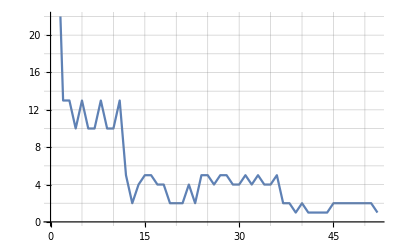

```mathematica
ListLinePlot[Table[(k/.repNullAtLeast),{k,nullAtoms}], GridLines->All]
```

```mathematica
Table[(k/.repNullAtLeast),{k,nullAtoms}]//DeleteDuplicates
```

{34,13,10,5,2,4,1}

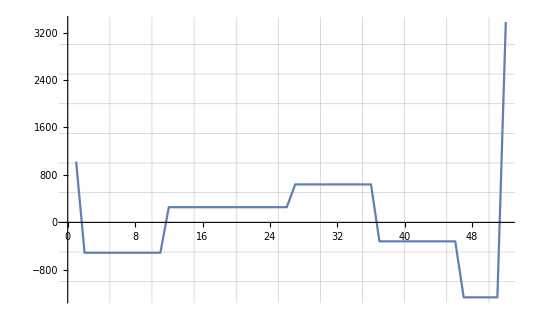

```mathematica
ListLinePlot[Table[NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]//Total, GridLines->All]
```

```mathematica
NullCoeff[allGraphs5[alfa1Key,"colofourrealnull"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,2}

```mathematica
Total[
Table[
NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]

]
```

{0,0,0,1,0,1,1,0,1,1,0,0,-2,-1,0,0,-1,-1,-2,-2,-2,-1,-2,0,0,-1,-1,-1,-2,-2,-1,-2,-1,-2,-2,-1,1,1,4,1,4,4,4,4,1,1,6,6,6,6,6,-30}

```mathematica
Total[
Table[
NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]

]
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,-2,-2,-2,0,0,-1,-1,-1,-1,-1,10}

```mathematica
sum=Total[
Table[
NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]

]+Total[
Table[
NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]

]
```

{0,0,0,1,0,1,1,0,1,1,0,0,-1,-1,0,0,-1,-1,-1,-1,-1,-1,-1,0,0,-1,-1,-1,-2,-2,-1,-2,-1,-2,-2,-1,1,1,2,1,2,2,2,2,1,1,5,5,5,5,5,-20}

```mathematica
Select[Keys[allGraphs5],NullCoeff[allGraphs5[#,"colofourrealnull"]]==sum&]
```

{}

```mathematica
atleast=Table[k/.repNullAtLeast,{k,nullAtoms}]
```

{34,13,13,10,13,10,10,13,10,10,13,5,2,4,5,5,4,4,2,2,2,4,2,5,5,4,5,5,4,4,5,4,5,4,4,5,2,2,1,2,1,1,1,1,2,2,2,2,2,2,2,1}

```mathematica
sum.atleast
```

5

```mathematica
Table[allGraphs5[k,"atmost"]=ChromaticPolynomial[allGraphs5[k,"graph"],4],{k,Keys[allGraphs5]}]
```

{1024,768,576,432,324,216,144,96,48,24,0,24,24,24,48,24,24,48,24,48,48,48,48,24,24,72,48,24,48,72,48,96,72,96,72,48,24,24,24,48,144,96,48,24,48,72,72,48,72,96,72,48,144,96,48,48,96,144,96,144,72,108,72,48,24,24,24,48,36,24,12,72,48,36,72,36,216,144,96,72,24,48,48,96,48,72,72,72,48,144,96,48,48,96,144,96,72,144,108,72,48,36,72,36,216,144,96,48,96,72,48,144,96,144,108,72,36,216,144,72,72,72,144,108,72,36,216,144,108,216,108,108,72,48,24,24,24,48,36,24,12,72,48,36,72,36,288,192,144,72,48,24,48,72,48,96,72,96,96,72,48,72,96,72,144,120,144,96,72,48,72,216,144,96,72,120,144,120,168,192,144,96,144,216,168,216,144,96,72,48,72,48,36,108,84,108,288,216,144,120,72,96,168,120,144,192,144,96,144,216,168,216,144,108,84,108,324,216,168,120,168,108,84,252,204,252,288,216,144,216,144,108,324,252,324,144,108,72,48,24,24,24,48,36,24,12,72,48,36,72,36,36,24,12,96,72,48,72,48,36,108,84,108,432,288,216,144,96,48,24,48,72,72,48,72,96,72,48,144,96,72,120,144,120,168,192,144,72,48,72,120,96,72,96,144,96,72,216,144,96,168,192,144,216,144,108,72,48,36,84,96,72,48,108,324,216,168,120,72,120,144,96,144,108,84,252,168,120,84,204,216,168,108,252,288,216,144,96,168,192,144,216,144,108,324,216,144,108,252,288,216,144,324,144,96,72,48,72,48,36,108,84,108,384,288,216,144,96,48,48,96,144,96,144,72,192,144,96,144,216,168,216,288,216,144,96,168,192,144,216,288,216,144,72,216,288,216,288,96,192,144,108,72,36,108,144,108,144,48,432,324,252,204,120,84,168,252,168,216,108,336,252,168,252,324,240,324,432,324,252,168,240,336,252,324,432,324,216,108,324,432,324,432,144,192,144,108,72,48,24,24,24,48,36,24,12,72,48,36,72,36,36,24,12,96,72,48,72,48,36,108,84,108,48,36,24,12,12,36,144,108,72,48,36,84,96,72,48,108,48,36,144,108,72,36,108,144,108,144,48,576,432,324,216,144,96,72,24,48,48,96,48,72,72,72,48,144,120,72,96,168,120,144,108,72,48,36,84,216,168,120,72,120,144,96,144,108,84,252,204,120,84,168,252,168,216,108,288,192,144,120,48,72,72,144,72,96,96,96,72,216,168,96,144,216,144,192,144,96,72,48,108,288,216,168,96,144,216,144,192,144,108,324,252,144,108,216,324,216,288,144,144,108,72,48,36,84,96,72,48,108,432,288,216,144,96,48,48,96,144,96,72,144,192,144,96,144,216,168,216,144,108,72,36,108,324,252,168,120,84,204,216,168,108,252,336,252,168,252,324,240,324,384,288,216,168,96,144,216,144,192,288,216,144,72,216,288,216,96,288,192,144,108,144,48,432,324,240,168,252,324,252,336,432,324,216,108,324,432,324,144,432,192,144,108,72,48,36,84,96,72,48,108,48,36,144,108,72,36,108,144,108,144,48,576,432,324,216,144,96,48,96,72,48,144,96,144,108,72,36,216,168,120,168,108,84,252,204,252,288,216,144,96,168,192,144,216,144,108,324,252,168,240,336,252,324,432,288,216,168,96,144,216,144,192,144,108,324,240,168,252,324,252,336,384,288,216,144,216,96,72,288,216,288,192,144,48,432,324,216,324,144,108,432,324,432,192,144,108,72,36,108,144,108,144,48,576,432,324,216,144,72,72,72,144,108,72,36,216,144,108,216,108,288,216,144,216,144,108,324,252,324,432,324,216,144,108,252,288,216,144,324,432,324,216,108,324,432,324,432,144,576,432,324,252,144,108,216,324,216,288,144,432,324,216,108,324,432,324,144,432,576,432,324,216,324,144,108,432,324,432,576,432,288,144,144,432,192,144,48,576,432,192,576,192,256,192,144,108,72,48,24,24,24,48,36,24,12,72,48,36,72,36,36,24,12,96,72,48,72,48,36,108,84,108,48,36,24,12,12,36,144,108,72,48,36,84,96,72,48,108,48,36,144,108,72,36,108,144,108,144,48,64,48,36,24,12,12,36,16,12,4,48,36,16,48,16,192,144,108,84,48,36,72,108,72,96,48,48,36,144,108,72,36,108,144,108,48,144,64,48,36,16,48,16,192,144,108,72,108,48,36,144,108,144,64,48,16,192,144,96,48,48,144,64,48,16,192,144,64,192,64,768,576,432,324,252,204,120,72,24,48,48,72,84,48,36,120,72,84,120,84,144,96,48,96,108,72,168,120,168,252,168,96,48,72,120,144,96,108,168,216,144,72,72,144,216,144,216,108,324,252,168,120,48,72,96,168,96,144,108,216,144,72,72,144,216,144,108,216,324,216,144,72,144,108,72,216,144,216,288,192,96,96,96,192,144,96,48,288,192,144,288,144,144,108,84,48,36,72,108,72,96,48,432,336,252,144,96,48,96,108,72,168,120,168,84,48,36,192,144,96,144,144,108,252,204,252,324,216,144,96,168,216,168,240,108,72,288,216,144,216,324,252,324,432,324,216,168,96,144,240,168,216,108,72,288,216,144,216,324,252,324,432,288,216,144,216,144,108,324,252,324,144,96,48,384,288,192,288,192,144,432,336,432,192,144,108,84,48,36,72,108,72,96,48,48,36,144,108,72,36,108,144,108,48,144,576,432,324,252,168,96,48,72,120,144,96,108,168,216,144,96,168,216,168,240,108,84,48,36,72,336,252,144,96,108,204,192,144,144,252,324,216,144,252,288,216,324,432,324,240,168,96,168,216,144,216,324,216,144,108,252,288,216,144,324,144,108,72,96,48,432,324,216,144,252,288,216,324,432,288,192,144,336,384,288,192,432,192,144,108,72,36,108,144,108,48,144,576,432,324,216,144,72,72,144,216,144,216,108,108,72,288,216,144,216,324,252,324,144,108,72,36,108,432,324,216,144,252,288,216,324,144,108,432,324,216,108,324,432,324,432,144,576,432,324,252,144,108,216,324,216,288,144,144,108,432,324,216,324,432,324,432,192,144,108,48,144,576,432,324,216,324,432,324,432,192,144,576,432,288,144,432,576,432,576,192,256,192,144,108,84,48,36,72,108,72,96,48,48,36,144,108,72,36,108,144,108,48,144,64,48,36,16,48,16,192,144,108,72,108,48,36,144,108,144,64,48,16,192,144,96,48,48,144,64,48,16,192,144,64,192,64,768,576,432,324,252,168,120,48,72,96,168,96,144,108,216,168,96,144,240,168,216,324,240,168,96,168,216,144,216,324,252,144,108,216,324,216,288,144,144,108,84,48,36,72,108,72,96,48,432,336,252,204,96,108,144,252,144,192,144,324,252,144,216,324,216,288,432,324,252,144,216,324,216,288,432,336,192,144,288,432,288,384,192,192,144,108,72,108,48,36,144,108,144,576,432,324,216,144,72,72,144,216,144,108,216,108,72,288,216,144,216,324,252,324,432,324,216,144,108,252,288,216,144,324,144,108,432,324,216,324,432,324,432,192,144,108,72,36,108,144,108,48,144,576,432,324,252,144,216,324,216,288,144,108,432,324,216,108,324,432,324,144,432,576,432,324,216,324,432,324,432,192,144,576,432,288,144,432,576,432,192,576,256,192,144,108,72,108,48,36,144,108,144,64,48,16,192,144,96,48,48,144,64,48,16,192,144,64,192,64,768,576,432,324,216,144,72,144,108,72,216,144,216,288,216,144,216,144,108,324,252,324,144,108,72,108,432,324,216,144,252,288,216,324,432,324,216,324,432,324,432,192,144,108,72,108,48,36,144,108,144,576,432,324,252,144,216,324,216,288,432,324,216,324,432,324,432,192,144,108,144,576,432,324,216,324,144,108,432,324,432,576,432,288,432,192,144,576,432,576,256,192,144,96,48,48,144,64,48,16,192,144,64,192,64,768,576,432,288,192,96,96,96,192,144,96,48,288,192,144,288,144,144,96,48,384,288,192,288,192,144,432,336,432,192,144,96,48,48,144,576,432,288,192,144,336,384,288,192,432,192,144,576,432,288,144,432,576,432,576,192,256,192,144,96,48,48,144,64,48,16,192,144,64,192,64,768,576,432,336,192,144,288,432,288,384,192,192,144,576,432,288,144,432,576,432,192,576,256,192,144,64,192,64,768,576,432,288,432,192,144,576,432,576,256,192,64,768,576,384,192,192,576,256,192,64,768,576,256,768,256}

```mathematica
eqs=Fold[And,Table[allGraphs5[k,"atleast"]a≤allGraphs5[k,"colofourrealnull"] ≤ allGraphs5[k,"atmost"]a,{k,allGraphs5AtomKeys}]]
```

0≤24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5≤0&&0≤-6 n12345+2 n123x45+2 n1245x3+n12x345-n12x3x45+2 n1345x2+n13x245-n13x2x45+n145x23-n145x2x3+2 n1x2345-n1x23x45-n1x245x3-n1x2x345+n1x2x3x45≤24 a&&0≤-6 n12345+2 n1235x4+2 n124x35+n12x345-n12x35x4+2 n1345x2+n135x24-n135x2x4+n14x235-n14x2x35+2 n1x2345-n1x235x4-n1x24x35-n1x2x345+n1x2x35x4≤24 a&&0≤-6 n12345+2 n1234x5+2 n125x34+n12x345-n12x34x5+2 n1345x2+n134x25-n134x2x5+n15x234-n15x2x34+2 n1x2345-n1x234x5-n1x25x34-n1x2x345+n1x2x34x5≤24 a&&a≤2 n12345-n12x345-n1345x2-n1x2345+n1x2x345≤24 a&&0≤-6 n12345+2 n1235x4+2 n1245x3+n125x34-n125x3x4+2 n134x25+n13x245-n13x25x4+n14x235-n14x25x3+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4≤24 a&&0≤2 n12345-n125x34-n134x25-n1x2345+n1x25x34≤24 a&&0≤-6 n12345+2 n1234x5+2 n1245x3+n124x35-n124x3x5+2 n135x24+n13x245-n13x24x5+n15x234-n15x24x3+2 n1x2345-n1x234x5-n1x245x3-n1x24x35+n1x24x3x5≤24 a&&0≤2 n12345-n124x35-n135x24-n1x2345+n1x24x35≤24 a&&0≤2 n12345-n1245x3-n13x245-n1x2345+n1x245x3≤24 a&&0≤-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n145x23+n14x235-n14x23x5+n15x234-n15x23x4+2 n1x2345-n1x234x5-n1x235x4-n1x23x45+n1x23x4x5≤24 a&&a≤2 n12345-n123x45-n145x23-n1x2345+n1x23x45≤24 a&&0≤2 n12345-n1235x4-n14x235-n1x2345+n1x235x4≤24 a&&a≤2 n12345-n1234x5-n15x234-n1x2345+n1x234x5≤24 a&&a≤-n12345+n1x2345≤12 a&&0≤-6 n12345+2 n1235x4+2 n1245x3+n125x34-n125x3x4+2 n1345x2+n135x24-n135x2x4+n145x23-n145x2x3+2 n15x234-n15x23x4-n15x24x3-n15x2x34+n15x2x3x4≤24 a&&a≤2 n12345-n125x34-n1345x2-n15x234+n15x2x34≤24 a&&0≤2 n12345-n1245x3-n135x24-n15x234+n15x24x3≤24 a&&a≤2 n12345-n1235x4-n145x23-n15x234+n15x23x4≤24 a&&a≤-n12345+n15x234≤12 a&&0≤-6 n12345+2 n1234x5+2 n1245x3+n124x35-n124x3x5+2 n1345x2+n134x25-n134x2x5+n145x23-n145x2x3+2 n14x235-n14x23x5-n14x25x3-n14x2x35+n14x2x3x5≤24 a&&0≤2 n12345-n124x35-n1345x2-n14x235+n14x2x35≤24 a&&0≤2 n12345-n1245x3-n134x25-n14x235+n14x25x3≤24 a&&0≤2 n12345-n1234x5-n145x23-n14x235+n14x23x5≤24 a&&0≤-n12345+n14x235≤12 a&&a≤2 n12345-n1245x3-n1345x2-n145x23+n145x2x3≤24 a&&a≤-n12345+n145x23≤12 a&&0≤-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5≤24 a&&0≤2 n12345-n123x45-n1345x2-n13x245+n13x2x45≤24 a&&0≤2 n12345-n1235x4-n134x25-n13x245+n13x25x4≤24 a&&0≤2 n12345-n1234x5-n135x24-n13x245+n13x24x5≤24 a&&0≤-n12345+n13x245≤12 a&&0≤2 n12345-n1235x4-n1345x2-n135x24+n135x2x4≤24 a&&0≤-n12345+n135x24≤12 a&&0≤2 n12345-n1234x5-n1345x2-n134x25+n134x2x5≤24 a&&0≤-n12345+n134x25≤12 a&&a≤-n12345+n1345x2≤12 a&&0≤-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1245x3+n124x35-n124x3x5+n125x34-n125x3x4+2 n12x345-n12x34x5-n12x35x4-n12x3x45+n12x3x4x5≤24 a&&a≤2 n12345-n123x45-n1245x3-n12x345+n12x3x45≤24 a&&0≤2 n12345-n1235x4-n124x35-n12x345+n12x35x4≤24 a&&a≤2 n12345-n1234x5-n125x34-n12x345+n12x34x5≤24 a&&a≤-n12345+n12x345≤12 a&&a≤2 n12345-n1235x4-n1245x3-n125x34+n125x3x4≤24 a&&a≤-n12345+n125x34≤12 a&&0≤2 n12345-n1234x5-n1245x3-n124x35+n124x3x5≤24 a&&0≤-n12345+n124x35≤12 a&&a≤-n12345+n1245x3≤12 a&&a≤2 n12345-n1234x5-n1235x4-n123x45+n123x4x5≤24 a&&a≤-n12345+n123x45≤12 a&&a≤-n12345+n1235x4≤12 a&&a≤-n12345+n1234x5≤12 a&&a≤n12345≤4 a

```mathematica
eqs[[1]]
```

34 a≤n1x2x3x4x5≤1024 a

```mathematica
Chrom[k_]:=Chrom[k]=ChromaticPolynomial[allGraphs5[k,"graph"],4]
```

```mathematica
Reduce[eqs,a]
```

```mathematica
Table[With[{a=allGraphs5[k,"embed"],b=allGraphs5[0,"embed"]},{a,b,b Chrom[k]/Chrom[0]}] ,{k,allGraphs5AtomKeys}]
```

{{0,628,0},{10,628,471/32},{6,628,471/32},{20,628,471/32},{14,628,471/32},{11,628,471/32},{31,628,471/32},{6,628,471/32},{0,628,471/32},{10,628,471/32},{10,628,471/32},{14,628,471/32},{10,628,471/32},{14,628,471/32},{11,628,471/64},{11,628,471/32},{29,628,471/32},{8,628,471/32},{16,628,471/32},{11,628,471/64},{9,628,471/32},{3,628,471/32},{8,628,471/32},{8,628,471/32},{4,628,471/64},{20,628,471/32},{12,628,471/64},{9,628,471/32},{8,628,471/32},{8,628,471/32},{3,628,471/32},{4,628,471/64},{13,628,471/32},{5,628,471/64},{7,628,471/32},{9,628,471/64},{16,628,471/64},{11,628,471/32},{16,628,471/32},{8,628,471/32},{29,628,471/32},{11,628,471/64},{21,628,471/32},{26,628,471/64},{13,628,471/32},{5,628,471/64},{18,628,471/64},{20,628,471/32},{12,628,471/64},{18,628,471/64},{16,628,471/64},{16,628,157/64}}

```mathematica
NullCoeff6[allGraphs6[alfa1Key,"colofourrealnull"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0}

```mathematica
NullCoeff6[allGraphs6[quad1Key,"colofourrealnull"]]
```

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,0,0,0,0,0,0}

```mathematica
repNull=Table[allGraphs5[k,"colofourrealnull"]->Style[VertexCount[allGraphs5[k,"graph"]],Red],{k,allGraphs5NullAtomKeys}];
```

```mathematica
MatrixPlot[Table[NullCoeff[allGraphs5[k,"colofournull"]],{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]]
```

-Graphics-

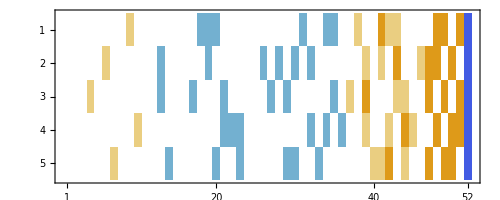

```mathematica
MatrixPlot[Table[NullCoeff[allGraphs5[k,"colofourrealnull"]],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]
```

```mathematica
Table[allGraphs5[k,"colofourrealnull"]/.repNull,{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total
```

-30 1+55 2-30 3+5 4

```mathematica
Total[Table[allGraphs5[k,"colofourrealnull"]/.repNull,{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]]+ Total[Table[allGraphs5[k,"colofourrealnull"]/.repNull,{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]
```

-20 1+40 2-25 3+5 4

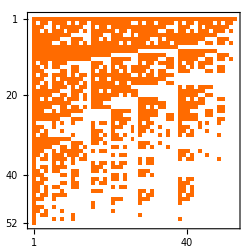

```mathematica
MatrixPlot[Table[FakeNullCoeff[allGraphs5[k,"colofournull"]],{k,allGraphs5AtomKeys}]//Inverse]
```

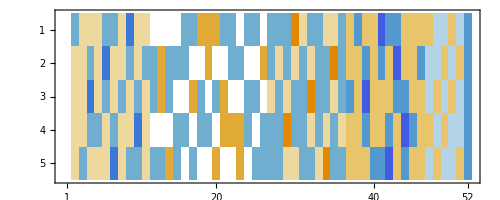

```mathematica
MatrixPlot[Table[FakeNullCoeff[allGraphs5[k,"colofournull"]],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]
```

```mathematica
TableForm[Table[FakeNullCoeff[allGraphs5[k,"colofournull"]],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total, TableDirections->Row]
```

0 | 1/2 | 1/2 | -1/2 | 1/2 | -1/2 | -1/2 | 1/2 | -1/2 | -1/2 | 1/2 | -1/2 | 1/2 | 0 | -1/2 | -1/2 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 1/2 | -1/2 | -1/2 | 0 | -1/2 | -1/2 | 1/2 | 1/2 | -1/2 | 1/2 | -1/2 | 1/2 | 1/2 | -1/2 | 3/4 | 3/4 | -3/4 | 3/4 | -3/4 | -3/4 | -3/4 | -3/4 | 3/4 | 3/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -5/4

```mathematica
TableForm[Table[FakeNullCoeff[allGraphs5[k,"colofournull"]],{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]//Total, TableDirections->Row]
```

0 | -1/2 | -1/2 | 1/2 | -1/2 | 1/2 | 1/2 | -1/2 | 1/2 | 1/2 | -1/2 | 2/3 | -1/3 | -1/3 | 2/3 | 2/3 | -1/3 | -1/3 | -1/3 | -1/3 | -1/3 | -1/3 | -1/3 | 2/3 | 2/3 | -1/3 | 1/2 | 1/2 | -1/2 | -1/2 | 1/2 | -1/2 | 1/2 | -1/2 | -1/2 | 1/2 | -5/12 | -5/12 | 7/12 | -5/12 | 7/12 | 7/12 | 7/12 | 7/12 | -5/12 | -5/12 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | 5/12

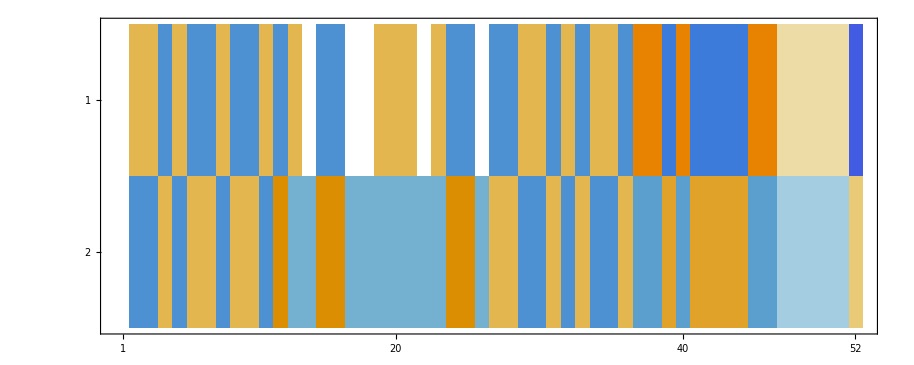

```mathematica
MatrixPlot[{
Table[FakeNullCoeff[allGraphs5[k,"colofournull"]],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total,
Table[FakeNullCoeff[allGraphs5[k,"colofournull"]],{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]//Total
}]
```

```mathematica
repFake=Table[allGraphs5[k,"colofournull"]->ShowGraph5Least[k],{k,allGraphs5FakeAtomKeys}]
```

{p1x2x3x4x5→-Graphics-034,p12x3x4x5→-Graphics-1968321,p12345→-Graphics-295240,p1234x5→-Graphics-287640,p1235x4→-Graphics-272460,p123x4x5→-Graphics-264878,p123x45→-Graphics-264885,p1245x3→-Graphics-227080,p124x3x5→-Graphics-219519,p124x35→-Graphics-219545,p125x3x4→-Graphics-204398,p125x34→-Graphics-204485,p12x34x5→-Graphics-1969213,p12x345→-Graphics-196965,p12x35x4→-Graphics-1968615,p12x3x45→-Graphics-1968413,p13x2x4x5→-Graphics-656124,p1345x2→-Graphics-94900,p134x25→-Graphics-87845,p134x2x5→-Graphics-87579,p135x24→-Graphics-73745,p135x2x4→-Graphics-72939,p13x24x5→-Graphics-664216,p13x245→-Graphics-66705,p13x25x4→-Graphics-658816,p13x2x45→-Graphics-656215,p14x2x3x5→-Graphics-218724,p145x23→-Graphics-31605,p145x2x3→-Graphics-29178,p14x23x5→-Graphics-243015,p14x235→-Graphics-24605,p14x25x3→-Graphics-221416,p14x2x35→-Graphics-219016,p15x2x3x4→-Graphics-72921,p15x23x4→-Graphics-97213,p15x234→-Graphics-10625,p15x24x3→-Graphics-81015,p15x2x34→-Graphics-73813,p1x23x4x5→-Graphics-24321,p1x2345→-Graphics-3640,p1x234x5→-Graphics-3338,p1x235x4→-Graphics-2739,p1x23x45→-Graphics-24413,p1x24x3x5→-Graphics-8124,p1x245x3→-Graphics-1099,p1x24x35→-Graphics-8416,p1x25x3x4→-Graphics-2724,p1x25x34→-Graphics-3615,p1x2x34x5→-Graphics-921,p1x2x345→-Graphics-138,p1x2x35x4→-Graphics-324,p1x2x3x45→-Graphics-121}

```mathematica
(24*Table[allGraphs5[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]//Total//Simplify//Expand)/.repFake
```

4 -Graphics-1969213-8 -Graphics-1968615+4 -Graphics-1968413+4 -Graphics-664216+4 -Graphics-658816-8 -Graphics-656215-8 -Graphics-243015+4 -Graphics-221416+4 -Graphics-219016+4 -Graphics-97213-8 -Graphics-81015+4 -Graphics-73813+4 -Graphics-24413+4 -Graphics-8416-8 -Graphics-3615+8 -Graphics-264885-4 -Graphics-219545+8 -Graphics-204485+8 -Graphics-196965-4 -Graphics-87845-4 -Graphics-73745-4 -Graphics-66705+8 -Graphics-31605-4 -Graphics-24605+8 -Graphics-10625-20 -Graphics-295240

```mathematica
(24*Table[allGraphs5[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total//Simplify//Expand)/.repFake
```

12 -Graphics-1968321-12 -Graphics-656124-12 -Graphics-218724+12 -Graphics-72921+12 -Graphics-24321-12 -Graphics-8124-12 -Graphics-2724+12 -Graphics-921-12 -Graphics-324+12 -Graphics-121-12 -Graphics-1969213-12 -Graphics-1968413+12 -Graphics-664216+12 -Graphics-658816+12 -Graphics-221416+12 -Graphics-219016-12 -Graphics-97213-12 -Graphics-73813-12 -Graphics-24413+12 -Graphics-8416-12 -Graphics-264878+12 -Graphics-219519-12 -Graphics-204398+12 -Graphics-87579+12 -Graphics-72939-12 -Graphics-29178-12 -Graphics-3338+12 -Graphics-2739+12 -Graphics-1099-12 -Graphics-138+18 -Graphics-264885-18 -Graphics-219545+18 -Graphics-204485+18 -Graphics-196965-18 -Graphics-87845-18 -Graphics-73745-18 -Graphics-66705+18 -Graphics-31605-18 -Graphics-24605+18 -Graphics-10625+6 -Graphics-287640+6 -Graphics-272460+6 -Graphics-227080+6 -Graphics-94900+6 -Graphics-3640-30 -Graphics-295240

```mathematica
(24*Table[allGraphs5[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]//Total//Simplify//Expand)/.repFake
```

-12 -Graphics-1968321+12 -Graphics-656124+12 -Graphics-218724-12 -Graphics-72921-12 -Graphics-24321+12 -Graphics-8124+12 -Graphics-2724-12 -Graphics-921+12 -Graphics-324-12 -Graphics-121+16 -Graphics-1969213-8 -Graphics-1968615+16 -Graphics-1968413-8 -Graphics-664216-8 -Graphics-658816-8 -Graphics-656215-8 -Graphics-243015-8 -Graphics-221416-8 -Graphics-219016+16 -Graphics-97213-8 -Graphics-81015+16 -Graphics-73813+16 -Graphics-24413-8 -Graphics-8416-8 -Graphics-3615+12 -Graphics-264878-12 -Graphics-219519+12 -Graphics-204398-12 -Graphics-87579-12 -Graphics-72939+12 -Graphics-29178+12 -Graphics-3338-12 -Graphics-2739-12 -Graphics-1099+12 -Graphics-138-10 -Graphics-264885+14 -Graphics-219545-10 -Graphics-204485-10 -Graphics-196965+14 -Graphics-87845+14 -Graphics-73745+14 -Graphics-66705-10 -Graphics-31605+14 -Graphics-24605-10 -Graphics-10625-6 -Graphics-287640-6 -Graphics-272460-6 -Graphics-227080-6 -Graphics-94900-6 -Graphics-3640+10 -Graphics-295240

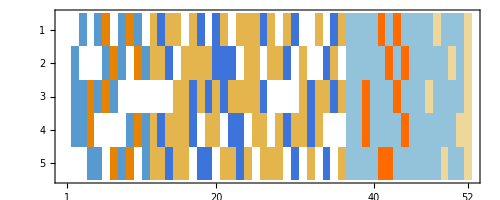

```mathematica
MatrixPlot[Table[FakeNullCoeff[allGraphs5[k,"colofournull"]],{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]]
```